```mathematica
Integrate[gy/(2 pi (gy^2 + (gx - 2 x)^2)), x, {gx - xp, gx}]
```

Integrate::ilim: Invalid integration variable or limit(s) in {gx-xp,gx}.

Integrate[gy/(2 pi (gy^2+(gx-2 x)^2)),x,{gx-xp,gx}]

```mathematica
Integrate[gy/(2 pi (gy^2 + (gx - 2 x)^2)), x, gx - xp ,gx]
```

Integrate::ilim: Invalid integration variable or limit(s) in gx-xp.

∫∫∫gy/(2 pi (gy^2+(gx-2 x)^2))ⅆgxⅆ(gx-xp)ⅆx

```mathematica
Integrate[gy/(2 pi (gy^2 + (gx - 2 x)^2)), {x, gx - xp, gx}]
```

ConditionalExpression[(ArcTan[gx/gy]-ArcTan[(gx-2 xp)/gy])/(4 pi),(Im[gy/xp]>Re[gx/xp]||2+Im[gy/xp]<Re[gx/xp]||Im[gx/xp]+Re[gy/xp]≠0)&&(Im[gy/xp]+Re[gx/xp]>2||Im[gy/xp]+Re[gx/xp]<0||Im[gx/xp]≠Re[gy/xp])]

```mathematica
(ArcTan[gx/gy]-ArcTan[(gx-2 xp)/gy])/(4 pi)
```

(ArcTan[gx/gy]-ArcTan[(gx-2 xp)/gy])/(4 pi)

```mathematica
gx=1
```

1

```mathematica
gy=1
```

1

```mathematica
xp = 0.5
```

0.5

```mathematica
In[4]
```

0.19635/pi

```mathematica
xp=.
```

```mathematica
pi=Pi
```

π

```mathematica
In[4]
```

(π/4-ArcTan[1-2 xp])/(4 π)

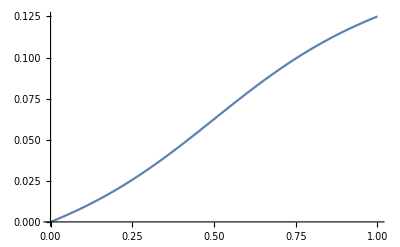

```mathematica
Plot[(π/4-ArcTan[1-2 xp])/(4 π),{xp,0,1}]
```

```mathematica
gy/(2 pi (gy^2 + (gx - 2 x)^2))
```

1/(2 π (1+(1-2 x)^2))

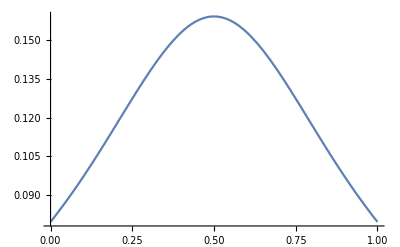

```mathematica
Plot[1/(2 π (1+(1-2 x)^2)),{x,0,1}]
```

```mathematica
gy/(2 pi (gy^2+(gx- x)^2))
```

1/(2 π (1+(1-x)^2))

```mathematica
gy/(2 pi (gy^2+(0.5-x)^2))
```

1/(2 π (1+(0.5-x)^2))

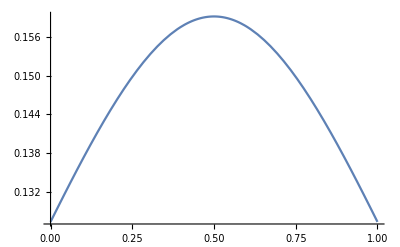

```mathematica
Plot[1/(2 π (1+(0.5-x)^2)),{x,0,1}]
```

```mathematica
1/(2 π (1+(0.5-x)^2)), {x->1}
```

```mathematica
1/(2 π (1+(0.5-x)^2))/.x->1
```

0.127324